```mathematica
"Dephasing with trace distance"
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];Clear[v0,v0ex,γ,w,p,f,vx,vy,vz,dv,vconstrained,hamiltonian];
γ=0.1;
v0ex = {1/Sqrt[3],1/Sqrt[3],1/Sqrt[3]};
w:={1,0,0};
p:={0,0,1}; (* Should be norm 1 *)
f[v0_] := (v0[[1]]-w[[1]])^2+(v0[[2]]-w[[2]])^2+(v0[[3]]-w[[3]])^2;
dv[h_,v_]:=2*Cross[h,v]-2γ({v[[1]],v[[2]],0});
hamiltonian[v_]:=-γ* Dot[v-Projection[v,p],w-v]* Cross[w,v]/Norm[Cross[w,v]]^2;
vsol = NDSolve[{vx'[t]==dv[hamiltonian[{vx[t],vy[t],vz[t]}],{vx[t],vy[t],vz[t]}][[1]],
vy'[t]==dv[hamiltonian[{vx[t],vy[t],vz[t]}],{vx[t],vy[t],vz[t]}][[2]],
vz'[t]==dv[hamiltonian[{vx[t],vy[t],vz[t]}],{vx[t],vy[t],vz[t]}][[3]],WhenEvent[Or[vx[t]<0,vy[t]<0,vz[t]<0],"StopIntegration"],{vx[0],vy[0],vz[0]}==v0ex},{vx,vy,vz},{t,0,30}];
domains=Function[x,InterpolatingFunctionDomain[First[x]]]/@First[{vx,vy,vz} /. vsol];
threshold=Min[Function[x,x[[1,1,2]]]/@domains];
sphere = ParametricPlot3D[{Cos[v]*Cos[u],Sin[v]*Cos[u],Sin[u]},{u,0,2*Pi},{v,-Pi/2,Pi/2},PlotStyle->None,MeshStyle->Gray,AxesLabel->{x,y,z}];
xyplane = ParametricPlot3D[{r*Cos[u],r*Sin[u],0},{u,0,2*Pi},{r,0,1},PlotStyle->{Opacity[0.2]}];
planetrajectory=ParametricPlot3D[{vx[t],vy[t],0}/.vsol,{t,0,threshold},PlotStyle->{Red,Opacity[0.5]}]/. Line[x_]:>{Arrowheads[{0.,0.03}],Arrow[x]};;
trajectory =ParametricPlot3D[{vx[t],vy[t],vz[t]}/.vsol,{t,0,threshold}]/. Line[x_]:>{Arrowheads[{0.,0.04,0.04}],Arrow[x]};
targetvector=ParametricPlot3D[{w[[1]]*t,w[[2]]*t,w[[3]]*t},{t,0,1},PlotStyle->{Orange,Opacity[0.5]}]/. Line[x_]:>{Arrowheads[{0.,0.04}],Arrow[x]};
Show[sphere,xyplane,planetrajectory,trajectory,targetvector]
Rasterize[Plot[Evaluate[{ hamiltonian[{vx[t],vy[t],vz[t]}][[1]], hamiltonian[{vx[t],vy[t],vz[t]}][[2]], hamiltonian[{vx[t],vy[t],vz[t]}][[3]],Norm[hamiltonian[{vx[t],vy[t],vz[t]}]]} /. vsol],{t,0,threshold},AxesLabel->{TraditionalForm[t],TraditionalForm[Abs[H]]},PlotLegends->{TraditionalForm[Subscript[H, x]],TraditionalForm[Subscript[H, y]],TraditionalForm[Subscript[H, z]],TraditionalForm[Abs[H]]},AxesOrigin->{0,0},GridLines->{{0,{threshold,Dashed}},{0}}]]
Plot[Evaluate[100-100*((vx[t]-w[[1]])^2+(vy[t]-w[[2]])^2+(vz[t]-w[[3]])^2)/f[v0ex]/.vsol],{t,0,threshold},AxesOrigin->{0,0},AxesLabel->{TraditionalForm[t],"%Error in f"}]
```

Dephasing with trace distance

-Graphics3D-

```mathematica
"Depolarising with trace distance"
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];Clear[v0,v0ex,γ,w,p,f,vx,vy,vz,dv,vconstrained,hamiltonian];
γ=0.1;
v0ex = {1/Sqrt[3],1/Sqrt[3],1/Sqrt[3]};
w:={1,0,0};
f[v0_] := (v0[[1]]-w[[1]])^2+(v0[[2]]-w[[2]])^2+(v0[[3]]-w[[3]])^2;
dv[h_,v_]:=2*Cross[h,v]-4γ/3 * v;
hamiltonian[v_]:=-2(γ/3)* Dot[v,w-v]* Cross[w,v]/Norm[Cross[w,v]]^2;
vsol = NDSolve[{vx'[t]==dv[hamiltonian[{vx[t],vy[t],vz[t]}],{vx[t],vy[t],vz[t]}][[1]],
vy'[t]==dv[hamiltonian[{vx[t],vy[t],vz[t]}],{vx[t],vy[t],vz[t]}][[2]],
vz'[t]==dv[hamiltonian[{vx[t],vy[t],vz[t]}],{vx[t],vy[t],vz[t]}][[3]],WhenEvent[Or[vx[t]<0,vy[t]<0,vz[t]<0],"StopIntegration"],{vx[0],vy[0],vz[0]}==v0ex},{vx,vy,vz},{t,0,30}];
domains=Function[x,InterpolatingFunctionDomain[First[x]]]/@First[{vx,vy,vz} /. vsol];
threshold=Min[Function[x,x[[1,1,2]]]/@domains];
sphere = ParametricPlot3D[{Cos[v]*Cos[u],Sin[v]*Cos[u],Sin[u]},{u,0,2*Pi},{v,-Pi/2,Pi/2},PlotStyle->None,MeshStyle->Gray,AxesLabel->{x,y,z}];
xyplane = ParametricPlot3D[{r*Cos[u],r*Sin[u],0},{u,0,2*Pi},{r,0,1},PlotStyle->{Opacity[0.2]}];
planetrajectory=ParametricPlot3D[{vx[t],vy[t],0}/.vsol,{t,0,threshold},PlotStyle->{Red,Opacity[0.5]}]/. Line[x_]:>{Arrowheads[{0.,0.03}],Arrow[x]};;
trajectory =ParametricPlot3D[{vx[t],vy[t],vz[t]}/.vsol,{t,0,threshold}]/. Line[x_]:>{Arrowheads[{0.,0.04,0.04}],Arrow[x]};
targetvector=ParametricPlot3D[{w[[1]]*t,w[[2]]*t,w[[3]]*t},{t,0,1},PlotStyle->{Orange,Opacity[0.5]}]/. Line[x_]:>{Arrowheads[{0.,0.04}],Arrow[x]};
Show[ParametricPlot3D[{1+Sqrt[f[v0ex]]*Cos[v]*Cos[u],Sqrt[f[v0ex]]*Sin[v]*Cos[u],Sqrt[f[v0ex]]*Sin[u]},{u,0,2*Pi},{v,-Pi/2,Pi/2},PlotStyle->None,MeshStyle->Gray,AxesLabel->{x,y,z}],xyplane,planetrajectory,trajectory,targetvector]
Rasterize[Plot[Evaluate[{ hamiltonian[{vx[t],vy[t],vz[t]}][[1]], hamiltonian[{vx[t],vy[t],vz[t]}][[2]], hamiltonian[{vx[t],vy[t],vz[t]}][[3]],Norm[hamiltonian[{vx[t],vy[t],vz[t]}]]} /. vsol],{t,0,threshold},AxesLabel->{TraditionalForm[t],TraditionalForm[Abs[H]]},PlotLegends->{TraditionalForm[Subscript[H, x]],TraditionalForm[Subscript[H, y]],TraditionalForm[Subscript[H, z]],TraditionalForm[Abs[H]]},AxesOrigin->{0,0},GridLines->{{0,{threshold,Dashed}}}]]
```

Depolarising with trace distance

NDSolve::ndsz: At t == 18.8871, step size is effectively zero; singularity or stiff system suspected.

-Graphics3D-

-Graphics-

Amplitude Damping with trace distance

-Graphics3D-

-Graphics-

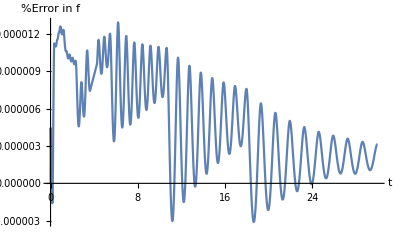

```mathematica
"Amplitude Damping with trace distance"
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];Clear[v0,v0ex,γ,w,p,f,vx,vy,vz,dv,vconstrained,vsol,hamiltonian];
γ=0.1;
v0ex = {1/Sqrt[3],1/Sqrt[3],1/Sqrt[3]};
w:={1,0,0};
p:={0,0,1}; (* Should be norm 1 *)
f[v0_] := (v0[[1]]-w[[1]])^2+(v0[[2]]-w[[2]])^2+(v0[[3]]-w[[3]])^2;
dv[h_,v_]:=2*Cross[h,v]-γ({v[[1]]/2,v[[2]]/2,v[[3]]-1});
hamiltonian[v_]:=(γ/4)* (Dot[v,v-w]+(v[[3]]-2)*(v[[3]]-w[[3]]))* Cross[w,v]/Norm[Cross[w,v]]^2;
vsol = NDSolve[{vx'[t]==dv[hamiltonian[{vx[t],vy[t],vz[t]}],{vx[t],vy[t],vz[t]}][[1]],
vy'[t]==dv[hamiltonian[{vx[t],vy[t],vz[t]}],{vx[t],vy[t],vz[t]}][[2]],
vz'[t]==dv[hamiltonian[{vx[t],vy[t],vz[t]}],{vx[t],vy[t],vz[t]}][[3]],WhenEvent[Or[vx[t]<0,vy[t]<0,vz[t]<0],"StopIntegration"],{vx[0],vy[0],vz[0]}==v0ex},{vx,vy,vz},{t,0,30}];
domains=Function[x,InterpolatingFunctionDomain[First[x]]]/@First[{vx,vy,vz} /. vsol];
threshold=Min[Function[x,x[[1,1,2]]]/@domains];
sphere = ParametricPlot3D[{Cos[v]*Cos[u],Sin[v]*Cos[u],Sin[u]},{u,0,2*Pi},{v,-Pi/2,Pi/2},PlotStyle->None,MeshStyle->Gray,AxesLabel->{x,y,z}];
xyplane = ParametricPlot3D[{r*Cos[u],r*Sin[u],0},{u,0,2*Pi},{r,0,1},PlotStyle->{Opacity[0.2]}];
planetrajectory=ParametricPlot3D[{vx[t],vy[t],0}/.vsol,{t,0,threshold},PlotStyle->{Red,Opacity[0.5]}]/. Line[x_]:>{Arrowheads[{0.,0.03}],Arrow[x]};;
trajectory =ParametricPlot3D[{vx[t],vy[t],vz[t]}/.vsol,{t,0,threshold}]/. Line[x_]:>{Arrowheads[{0.,0.04}],Arrow[x]};
targetvector=ParametricPlot3D[{w[[1]]*t,w[[2]]*t,w[[3]]*t},{t,0,1},PlotStyle->{Orange,Opacity[0.5]}]/. Line[x_]:>{Arrowheads[{0.,0.04}],Arrow[x]};
Show[sphere,xyplane,planetrajectory,trajectory,targetvector]
Rasterize[Plot[Evaluate[{ hamiltonian[{vx[t],vy[t],vz[t]}][[1]], hamiltonian[{vx[t],vy[t],vz[t]}][[2]], hamiltonian[{vx[t],vy[t],vz[t]}][[3]],Norm[hamiltonian[{vx[t],vy[t],vz[t]}]]} /. vsol],{t,0,threshold},AxesLabel->{TraditionalForm[t],TraditionalForm[Abs[H]]},PlotLegends->{TraditionalForm[Subscript[H, x]],TraditionalForm[Subscript[H, y]],TraditionalForm[Subscript[H, z]],TraditionalForm[Abs[H]]},AxesOrigin->{0,0},GridLines->{{0,{threshold,Dashed}},{0}}]]
Plot[Evaluate[100-100*((vx[t]-w[[1]])^2+(vy[t]-w[[2]])^2+(vz[t]-w[[3]])^2)/f[v0ex]/.vsol],{t,0,threshold},AxesOrigin->{0,0},AxesLabel->{TraditionalForm[t],"%Error in f"}]
```

```mathematica
"Dephasing with fidelity"
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];Clear[v0,v0ex,γ,w,p,f,vx,vy,vz,dv,vconstrained,hamiltonian];
γ=0.1;
v0ex = {1/Sqrt[3],1/Sqrt[3],1/Sqrt[3]};
w:={1,0,0};
p:={0,0,1}; (* Should be norm 1 *)
f[v0_] := 0.5*(1+Dot[v0,w]);
dv[h_,v_]:=2Cross[h,v]-2γ({v[[1]],v[[2]],0});
hamiltonian[v_]:=-γ* Dot[v-Projection[v,p],w]* Cross[w,v]/Norm[Cross[w,v]]^2;
vsol = NDSolve[{vx'[t]==dv[hamiltonian[{vx[t],vy[t],vz[t]}],{vx[t],vy[t],vz[t]}][[1]],
vy'[t]==dv[hamiltonian[{vx[t],vy[t],vz[t]}],{vx[t],vy[t],vz[t]}][[2]],
vz'[t]==dv[hamiltonian[{vx[t],vy[t],vz[t]}],{vx[t],vy[t],vz[t]}][[3]],WhenEvent[Or[vx[t]<0,vy[t]<0,vz[t]<0],"StopIntegration"],{vx[0],vy[0],vz[0]}==v0ex},{vx,vy,vz},{t,0,30}];
domains=Function[x,InterpolatingFunctionDomain[First[x]]]/@First[{vx,vy,vz} /. vsol];
threshold=Min[Function[x,x[[1,1,2]]]/@domains];
sphere = ParametricPlot3D[{Cos[v]*Cos[u],Sin[v]*Cos[u],Sin[u]},{u,0,2*Pi},{v,-Pi/2,Pi/2},PlotStyle->None,MeshStyle->Gray,AxesLabel->{x,y,z}];
xyplane = ParametricPlot3D[{r*Cos[u],r*Sin[u],0},{u,0,2*Pi},{r,0,1},PlotStyle->{Opacity[0.2]}];
planetrajectory=ParametricPlot3D[{vx[t],vy[t],0}/.vsol,{t,0,threshold},PlotStyle->{Red,Opacity[0.5]}]/. Line[x_]:>{Arrowheads[{0.,0.03}],Arrow[x]};;
trajectory =ParametricPlot3D[{vx[t],vy[t],vz[t]}/.vsol,{t,0,threshold}]/. Line[x_]:>{Arrowheads[{0.,0.04,0.04}],Arrow[x]};
targetvector=ParametricPlot3D[{w[[1]]*t,w[[2]]*t,w[[3]]*t},{t,0,1},PlotStyle->{Orange,Opacity[0.5]}]/. Line[x_]:>{Arrowheads[{0.,0.04}],Arrow[x]};
Show[sphere,xyplane,planetrajectory,trajectory,targetvector]
Rasterize[Plot[Evaluate[{ hamiltonian[{vx[t],vy[t],vz[t]}][[1]], hamiltonian[{vx[t],vy[t],vz[t]}][[2]], hamiltonian[{vx[t],vy[t],vz[t]}][[3]],Norm[hamiltonian[{vx[t],vy[t],vz[t]}]]} /. vsol],{t,0,threshold},AxesLabel->{TraditionalForm[t],TraditionalForm[Abs[H]]},PlotLegends->{TraditionalForm[Subscript[H, x]],TraditionalForm[Subscript[H, y]],TraditionalForm[Subscript[H, z]],TraditionalForm[Abs[H]]},AxesOrigin->{0,0},GridLines->{{0,{threshold,Dashed}},{0}}]]
```

Dephasing with fidelity

NDSolve::ndsz: At t == 3.7247, step size is effectively zero; singularity or stiff system suspected.

-Graphics3D-

-Graphics-

```mathematica
"Depolarising with fidelity"
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];Clear[v0,v0ex,γ,w,p,f,vx,vy,vz,dv,vconstrained,hamiltonian];
γ=0.1;
v0ex = {1/Sqrt[3],1/Sqrt[3],1/Sqrt[3]};
w:={1,0,0};
p:={0,0,1}; (* Should be norm 1 *)
f[v0_] := 0.5*(1+Dot[v0,w]);
dv[h_,v_]:=2Cross[h,v]-4γ*v/3;
hamiltonian[v_]:=-2γ/3* Dot[v-Projection[v,p],w]* Cross[w,v]/Norm[Cross[w,v]]^2;
vsol = NDSolve[{vx'[t]==dv[hamiltonian[{vx[t],vy[t],vz[t]}],{vx[t],vy[t],vz[t]}][[1]],
vy'[t]==dv[hamiltonian[{vx[t],vy[t],vz[t]}],{vx[t],vy[t],vz[t]}][[2]],
vz'[t]==dv[hamiltonian[{vx[t],vy[t],vz[t]}],{vx[t],vy[t],vz[t]}][[3]],WhenEvent[Or[vx[t]<0,vy[t]<0,vz[t]<0],"StopIntegration"],{vx[0],vy[0],vz[0]}==v0ex},{vx,vy,vz},{t,0,30}];
domains=Function[x,InterpolatingFunctionDomain[First[x]]]/@First[{vx,vy,vz} /. vsol];
threshold=Min[Function[x,x[[1,1,2]]]/@domains];
sphere = ParametricPlot3D[{Cos[v]*Cos[u],Sin[v]*Cos[u],Sin[u]},{u,0,2*Pi},{v,-Pi/2,Pi/2},PlotStyle->None,MeshStyle->Gray,AxesLabel->{x,y,z}];
xyplane = ParametricPlot3D[{r*Cos[u],r*Sin[u],0},{u,0,2*Pi},{r,0,1},PlotStyle->{Opacity[0.2]}];
planetrajectory=ParametricPlot3D[{vx[t],vy[t],0}/.vsol,{t,0,threshold},PlotStyle->{Red,Opacity[0.5]}]/. Line[x_]:>{Arrowheads[{0.,0.03}],Arrow[x]};;
trajectory =ParametricPlot3D[{vx[t],vy[t],vz[t]}/.vsol,{t,0,threshold}]/. Line[x_]:>{Arrowheads[{0.,0.04,0.04}],Arrow[x]};
targetvector=ParametricPlot3D[{w[[1]]*t,w[[2]]*t,w[[3]]*t},{t,0,1},PlotStyle->{Orange,Opacity[0.5]}]/. Line[x_]:>{Arrowheads[{0.,0.04}],Arrow[x]};
Show[sphere,xyplane,planetrajectory,trajectory,targetvector]
Rasterize[Plot[Evaluate[{ hamiltonian[{vx[t],vy[t],vz[t]}][[1]], hamiltonian[{vx[t],vy[t],vz[t]}][[2]], hamiltonian[{vx[t],vy[t],vz[t]}][[3]],Norm[hamiltonian[{vx[t],vy[t],vz[t]}]]} /. vsol],{t,0,threshold},AxesLabel->{TraditionalForm[t],TraditionalForm[Abs[H]]},PlotLegends->{TraditionalForm[Subscript[H, x]],TraditionalForm[Subscript[H, y]],TraditionalForm[Subscript[H, z]],TraditionalForm[Abs[H]]},AxesOrigin->{0,0},GridLines->{{0,{threshold,Dashed}},{0}}]]
```

Depolarising with fidelity

NDSolve::ndsz: At t == 4.11979, step size is effectively zero; singularity or stiff system suspected.

-Graphics3D-

-Graphics-

Amplitude Damping with fidelity

-Graphics3D-

-Graphics-

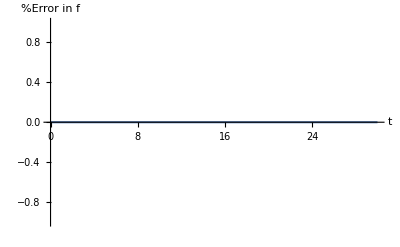

```mathematica
"Amplitude Damping with fidelity"
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];Clear[v0,v0ex,γ,w,p,f,vx,vy,vz,dv,vconstrained,vsol,hamiltonian];
γ=0.1;
v0ex = {1/Sqrt[3],1/Sqrt[3],1/Sqrt[3]};
w:={1,0,0};
p:={0,0,1}; (* Should be norm 1 *)
f[v0_] := 0.5*(1+Dot[v0,w]);
dv[h_,v_]:=2Cross[h,v]-γ({v[[1]]/2,v[[2]]/2,v[[3]]-1});
hamiltonian[v_]:=-γ/4* (Dot[v,w]+(v[[3]]-2)*w[[3]])* Cross[w,v]/Norm[Cross[w,v]]^2;
vsol = NDSolve[{vx'[t]==dv[hamiltonian[{vx[t],vy[t],vz[t]}],{vx[t],vy[t],vz[t]}][[1]],
vy'[t]==dv[hamiltonian[{vx[t],vy[t],vz[t]}],{vx[t],vy[t],vz[t]}][[2]],
vz'[t]==dv[hamiltonian[{vx[t],vy[t],vz[t]}],{vx[t],vy[t],vz[t]}][[3]],WhenEvent[Or[vx[t]<0,vy[t]<0,vz[t]<0],"StopIntegration"],{vx[0],vy[0],vz[0]}==v0ex},{vx,vy,vz},{t,0,30}];
domains=Function[x,InterpolatingFunctionDomain[First[x]]]/@First[{vx,vy,vz} /. vsol];
threshold=Min[Function[x,x[[1,1,2]]]/@domains];
sphere = ParametricPlot3D[{Cos[v]*Cos[u],Sin[v]*Cos[u],Sin[u]},{u,0,2*Pi},{v,-Pi/2,Pi/2},PlotStyle->None,MeshStyle->Gray,AxesLabel->{x,y,z}];
xyplane = ParametricPlot3D[{r*Cos[u],r*Sin[u],0},{u,0,2*Pi},{r,0,1},PlotStyle->{Opacity[0.2]}];
planetrajectory=ParametricPlot3D[{vx[t],vy[t],0}/.vsol,{t,0,threshold},PlotStyle->{Red,Opacity[0.5]}]/. Line[x_]:>{Arrowheads[{0.,0.03}],Arrow[x]};;
trajectory =ParametricPlot3D[{vx[t],vy[t],vz[t]}/.vsol,{t,0,threshold}]/. Line[x_]:>{Arrowheads[{0.,0.04}],Arrow[x]};
targetvector=ParametricPlot3D[{w[[1]]*t,w[[2]]*t,w[[3]]*t},{t,0,1},PlotStyle->{Orange,Opacity[0.5]}]/. Line[x_]:>{Arrowheads[{0.,0.04}],Arrow[x]};
Show[sphere,xyplane,planetrajectory,trajectory,targetvector]
Rasterize[Plot[Evaluate[{ hamiltonian[{vx[t],vy[t],vz[t]}][[1]], hamiltonian[{vx[t],vy[t],vz[t]}][[2]], hamiltonian[{vx[t],vy[t],vz[t]}][[3]],Norm[hamiltonian[{vx[t],vy[t],vz[t]}]]} /. vsol],{t,0,threshold},AxesLabel->{TraditionalForm[t],TraditionalForm[Abs[H]]},PlotLegends->{TraditionalForm[Subscript[H, x]],TraditionalForm[Subscript[H, y]],TraditionalForm[Subscript[H, z]],TraditionalForm[Abs[H]]},AxesOrigin->{0,0},GridLines->{{0,{threshold,Dashed}},{0}}]]
Plot[Evaluate[100-100*f[{vx[t],vy[t],vz[t]}]/f[v0ex]/.vsol],{t,0,threshold},AxesOrigin->{0,0},AxesLabel->{TraditionalForm[t],"%Error in f"}]
```